```mathematica
AbsoluteTiming[Zeta[2]]
```

{0.0000698,π^2/6}

```mathematica
Sum[1/n^2,{n,1,∞}]
```

π^2/6

```mathematica
κ[x_,y_]={4+y^3,4x-x^3}
```

```mathematica
int1=Integrate[1/(4+y^3),y];
```

```mathematica
int2=Integrate[4x-x^3,x]
```

2 x^2-x^4/4

```mathematica
solveOne=Solve[int1==int2+c,c]
```

{{c→1/24 (-48 x^2+6 x^4+2 2^(2/3) √3 ArcTan[(-1+2^(1/3) y)/(√3)]+2 2^(2/3) Log[2+2^(1/3) y]-2^(2/3) Log[4-2 2^(1/3) y+2^(2/3) y^2])}}

```mathematica
g[x_,y_]=solveOne[[1,1,2]]
```

1/24 (-48 x^2+6 x^4+2 2^(2/3) √3 ArcTan[(-1+2^(1/3) y)/(√3)]+2 2^(2/3) Log[2+2^(1/3) y]-2^(2/3) Log[4-2 2^(1/3) y+2^(2/3) y^2])

```mathematica
g[x,y]
```

1/24 (-48 x^2+6 x^4+2 2^(2/3) √3 ArcTan[(-1+2^(1/3) y)/(√3)]+2 2^(2/3) Log[2+2^(1/3) y]-2^(2/3) Log[4-2 2^(1/3) y+2^(2/3) y^2])

```mathematica
solDif=DSolve[y'[x]==(4x-x^3)/(4+y[x]^3),y[x],x];
```

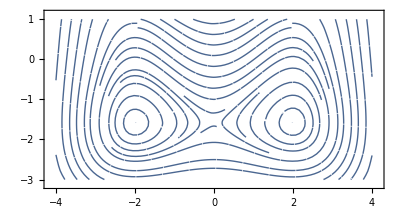

```mathematica
StreamPlot[κ[x,y],{x,-4,4},{y,-3,1},StreamStyle->{Arrowheads[0,Black]},AspectRatio->Automatic]
```

```mathematica
Table[Graphics[Arrow[{{Cos[t],0},{Cos[t],0}+.5{0,Cos[t]}}]],{t,0,2π,.3];
```

```mathematica
Manipulate[Show[ParametricPlot[{Cos[t],Sin[t]},{t,0,2π}],Graphics[Arrow[{{Cos[t],Sin[t]},{Cos[t],Sin[t]}+.5{-Sin[t],Cos[t]}}]],Graphics[Arrow[{{0,0},{Cos[t],Sin[t]}}]],Graphics[Arrow[{{0,0},{0,0}+.5{-Sin[t],0}}]]],{t,0,2π}]
```

```mathematica
Series[Exp[x],{x,0,5}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+O[x]^6

```mathematica
%[[5]]
```

6